```mathematica
<<ACPackages`
<<ACPackages`Master`
```

```mathematica
SetWorkDir["2010.08.15"]
```

D:\Programs\icmm\tormagn\2010.08.15

```mathematica
SetWorkDir[]
```

d:\home\Anton\programs\tormagn

```mathematica
SetWorkDir["Run"]
```

D:\Programs\icmm\tormagn\Run

```mathematica
$HistoryLength=0;
```

#### Разбор логов

```mathematica
text=Import["../message.dat","Text"];
```

```mathematica
StrMsg[msg_String]:="(?s)(message of proc#(\\d+) at )?t=(-?\\d+(\\.\\d+)?)\\s*Niter=(\\d+)\\s*time of work=\\d+(\\.\\d+)? sec:\\s*"<>msg
StrChg[par_String]:=StrMsg[par<>" was changed to"]
```

```mathematica
StrChg[par_String]:="t=(-?\\d+(\\.\\d+)?)\\s*Niter=(\\d+)\\s*time of work=\\d+(\\.\\d+)? sec:\\s*"<>par<>" was changed to";
```

```mathematica
Rmt=StringCases[text,RegularExpression[StrChg["Rm"]]:>ToExpression["$3"]];
```

```mathematica
StringCases[text,RegularExpression[StrMsg["(.*?)"]]:>"$0"]//Length
```

```mathematica
StringCases[text,RegularExpression[StrChg["rc"]]:>"$3"]
```

{0.6500,0.5500,0.4500,0.3500}

```mathematica
cs=StringCases[text,RegularExpression[StringJoin["(?s)(",StrChg["rc"],")?(.+?)(?=(",StrChg["rc"],")|$)"]]:>"$0"];cs={StringCases[#,RegularExpression[StrChg["rc"]]->"$3"],StringCases[#,RegularExpression[StrChg["Rm"]]->"$3"],StringCases[#,RegularExpression[StrMsg["snap is done"]]->"$5"]}&/@cs;
TableForm[{#⟦1⟧,#⟦3,-1⟧}&/@cs]
```

| 13954
0.6500 | 13023
0.5500 | 11946
0.4500 | 10693
0.3500 | 9142

```mathematica
cs[[12]]
```

```mathematica
StringCases[text,RegularExpression["t=(20(\\.\\d+)?)\\s*Niter=(\\d+)\\s*time of work=(\\d+(\\.\\d+)?) sec:\nsnap is done"]:>{"$1","$3","$4"}]
```

```mathematica
StringReplace[StringDrop["="<>StringJoin[#<>"+"&/@((%187)^ᵀ)[[3]]],-1],"."->","]
```

=688,917+732,954+723,446+739,469+745,263+728,915+757,292+739,571+888,042+16124,1+5995,71+1662,78+2411,28+1966,04+1843,18+972,732+951,614+1057,18+1348,6

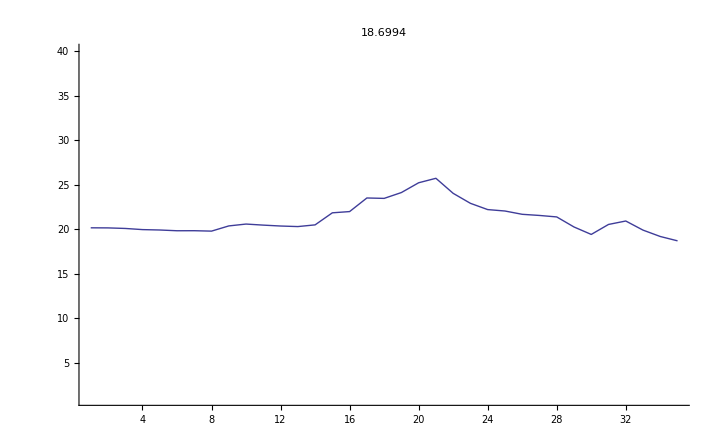

18.6994

```mathematica
ListPlot[Rmt,PlotRange->{1,40},PlotLabel->Last[Rmt],Joined->True]
Last[Rmt]
```

```mathematica
Select[Transpose[{Rmt,RotateLeft[Rmt]}],First[#]/Last[#]<1/2&]
```

General::stop: Further output of indet will be suppressed during this calculation.

{{53.6975,411.58},{53.7787,424.703},{54.0186,163.121},{54.4055,204.604},{54.9204,314.229},{55.5277,411.445},{56.1905,561.897},{56.8542,302.604},{0.,155.591},{59.3789,145.69},{3.4467,7.874},{0.1227,0.7669},{41.6201,134.853},{34.459,344.59},{28.9494,187.443},{28.997,64.8537},{2.8446,180.678}}

#### Графики по времени

```mathematica
Off[Thread::tdlen];
lv=ReadList["vv.dat"];lv=Map[{#⟦1,1⟧,#⟦2⟧}&,lv];
ltm=Flatten[First/@lv];
{Length[ltm],Last[ltm]}
```

```mathematica
PrintRange[{First[#],Max[Last[#]]}&/@lv,All,PlotLabel->"Maximum of stream velocity"]
```

```mathematica
Export["energy5.dat",Transpose@Join[{ltm},Map[Last,{mp,mdp,mvx,mdvx,mvy,mdvy,mvz,mdvz,mAx,mdAx,mAy,mdAy,mAz,mdAz,mBx,mBy,mBz,mqp,mqvx,mqvy,mqvz,mqAx,mqAy,mqAz,mqBx,mqBy,mqBz},{2}]]]
```

```mathematica
PrintRange[dif[ltm],All,PlotLabel->"Time step"]
PrintRange[{#⟦1⟧/3,#⟦2⟧}&/@(mqvx+mqvy+mqvz)]
```

```mathematica
Dynamic[Refresh[
len=Transpose[Select[Import["energy.dat","Table"],(0<First[#])&]];
ltm=First[len];
{mp,mdp,mvx,mdvx,mvy,mdvy,mvz,mdvz,mAx,mdAx,mAy,mdAy,mAz,mdAz,mBx,mBy,mBz,mqp,mqvx,mqvy,mqvz,mqAx,mqAy,mqAz,mqBx,mqBy,mqBz}=Transpose[{ltm,#}]&/@Drop[len,2];
PrintRange[{#⟦1⟧/3,Log[10,#⟦2⟧]}&/@(mqBx+mqBy+mqBz),All,
PlotLabel->"Last energy="<>ToString[Last[Last[mqBx+mqBy+mqBz]]]],UpdateInterval->5]
]
```

```mathematica
len=Transpose[Select[Import["energy(0.00).dat","Table"],(0<First[#])&]];
ltm=First[len];(*PrintRange[dif[ltm],All,PlotLabel->"Time step"]*)
{mp,mdp,mvx,mdvx,mvy,mdvy,mvz,mdvz,mAx,mdAx,mAy,mdAy,mAz,mdAz,mBx,mBy,mBz,mqp,mqvx,mqvy,mqvz,mqAx,mqAy,mqAz,mqBx,mqBy,mqBz}=Transpose[{ltm,#}]&/@Drop[len,2];
(*PrintRange[{#⟦1⟧/3,#⟦2⟧}&/@(mqvx+mqvy+mqvz)]*)
(*PrintRange[{#⟦1⟧/3,Log[10,#⟦2⟧]}&/@(mqAx+mqAy+mqAz),All,PlotLabel->"Last energy="<>ToString[Last[Last[mqAx+mqAy+mqAz]]]]*)
PrintRange[{#⟦1⟧/3,Log[10,#⟦2⟧]}&/@(mqBx+mqBy+mqBz),All,
PlotLabel->"Last energy="<>ToString[Last[Last[mqBx+mqBy+mqBz]]]]
```

```mathematica
HarmClearance[l_]:=Divide@@Take[Sort[Take[Abs@Fourier@l,Ceiling[Length[l]/2]]],-2]
```

```mathematica
out=.;ReadBinarySnapFile["screw_64_2363.snp",6,out,PrintInfo->None];
{coor,bounds}=ReadAuxFiles[{"coord"},ShiftVector->{0,0,0}];
{Bx,By,Bz}=rotd[Sequence@@Take[out,-3],3];
PrintRange[WithoutFict@Bx⟦10,All,25⟧]
PrintRange[Take[Abs@Fourier@WithoutFict@Bx⟦15,All,15⟧,14]]
-10Log[10,HarmClearance[WithoutFict@Bx⟦13,All,8⟧]]
```

```mathematica
EstimateBoundary/@{Bx,By,Bz}
```

{63.4129,410.987,127.973}

```mathematica
MapThread[PrintRange[#1,All,PlotLabel->#2]&,{{mqvx,mqvy,mqvz,mqp},{"Mean quadratic of vr","Mean quadratic of vϕ","Mean quadratic of vz","Mean quadratic of p"}}]
```

```mathematica
grs=MapThread[PrintRange[#1,All,PlotLabel->#2]&,{Map[Function[l,{l⟦1⟧,Log[l⟦2⟧]/2}],#]&/@{mqAx,mqAy,mqAz},{"Mean quadratic of Ar","Mean quadratic of Aϕ","Mean quadratic of Az"}}]
```

```mathematica
MapThread[PrintRange[#1,All,PlotLabel->#2]&,{Map[Function[l,{l⟦1⟧,Log[Abs[l⟦2⟧]]/2}],#]&/@{mdAx,mdAy,mdAz},{"Difference of Ar","Difference of Aϕ","Difference of Az"}}]
```

```mathematica
grs=MapThread[PrintRange[#1,0.01{-1,1},PlotLabel->#2]&,{dif[Map[Function[l,{l⟦1⟧,Log[l⟦2⟧]/2}],#]]&/@{mqBx,mqBy,mqBz},{"Mean quadratic of Br","Mean quadratic of Bϕ","Mean quadratic of Bz"}}]
```

```mathematica
grs=MapThread[PrintRange[#1,All,PlotLabel->#2]&,{Map[Function[l,{l⟦1⟧,Log[Abs[l⟦2⟧]]}],#]&/@{mAx,mAy,mAz},{"Maximum of Ar","Maximum of Aϕ","Maximum of Az"}}]
```

```mathematica
ListPlot[mBy]
```

```mathematica
grs=MapThread[PrintRange[#1,All,PlotLabel->#2]&,{Map[Function[l,{l⟦1⟧,Log[10,Abs[l⟦2⟧]]}],#]&/@{mBx,mBy,mBz},{"Maximum of Br","Maximum of Bϕ","Maximum of Bz"}}]
```

#### Чтение из файлов

```mathematica
Remove[PrintInfo]
```

```mathematica
{coor,bounds}=ReadAuxFiles[{"coord"},ShiftVector->{0,0,0},NumberOfRefs->4];
```

```mathematica
out=.;ReadBinarySnapFile["screw.dmp",8,out,PrintInfo->Debug];
```

{1,1,2}

{0.,0,32,32,32,1000.}

Length of read from binary=508288 and size of it=2033152 bytes

ghost=3

```mathematica
out=.;ReadBinarySnapFile["velocity.snp",4,out,PrintInfo->Debug];
```

{1,1,1}

{0.,0,64,64,64,3.14}

Length of read from binary=1372000 and size of it=5488000 bytes

ghost=3

```mathematica
{coor,bounds,node}=ReadAuxFiles[{"coord","node"},ShiftVector->{0,0,0},ProcDistrib->{1,1,1},NumberOfRefs->4];
```

```mathematica
GetCoor[a_,b_,n_,ghost_]:=Block[{dx},
dx=(b-a)/n;
Table[a+i dx,{i,0.5-ghost,n+ghost-0.5,1}]
]
```

```mathematica
κ=0;
parR=2;parRfl=1;lfi=2π/0.685;
coor=MapThread[GetCoor[#1,#2,#3,ghost]&,{{(-parR+parRfl/If[κ==0,∞]),0,-parR},{(parR+parRfl/If[κ==0,∞]),lfi,parR},Rest[Dimensions[out]]-2ghost}];
bounds={#[[ghost]]+#[[ghost+1]],#[[-ghost]]+#[[-ghost-1]]}/2&/@coor
```

```mathematica
out=.;ReadBinarySnapFile["induct_4_851.snp",6,out,PrintInfo->Debug];
{coor,bounds,node}=ReadAuxFiles[{"coord","node"},ShiftVector->{1/0.3,0,0},ProcDistrib->{2,1,2},NumberOfRefs->4];
Print[bounds];
```

{2,1,2}

{4.00284,851,32,5,32,10.}

Length of read from binary=127776 and size of it=511104 bytes

ghost=3

{{1.33333,5.33333},{0.,1.},{-2.,2.}}

```mathematica
If[Length[out]>6,out=Take[out,{2,-2}]];
```

```mathematica
out=.;ReadBinarySnapFiles["induct",".dmp",8,out,PrintInfo->None];
(*{vx,vy,vz,Ax,Ay,Az}=out;*)
{coor,bounds,node}=ReadAuxFiles[{"coord","node"},ShiftVector->{1/0.3,0,0},ProcDistrib->{2,1,2},NumberOfRefs->0];
```

```mathematica
out=.;ReadBinarySnapFile["velocity.snp",5,out,PrintInfo->None];
```

Выделение внутренней области

```mathematica
GetInner[ar_?ArrayQ]:=Block[{b},Switch[Length[Dimensions[ar]],3,Transpose[(node/.b_:>BitAnd[b,8])/8#&/@Transpose[ar]],2,(node/.b_:>BitAnd[b,8])/8 ar,_,$Failed]]
```

```mathematica
GetVacuum[ar_?ArrayQ]:=Block[{b},Switch[Length[Dimensions[ar]],3,Transpose[(1-(node/.b_:>BitAnd[b,8])/8)#&/@Transpose[ar]],2,(1-(node/.b_:>BitAnd[b,8])/8)ar,_,$Failed]]
```

```mathematica
{vxs,vys,vzs,ps,nuts}=GetInner/@{vx,vy,vz,p,nut};
```

```mathematica
bounds
```

{{18.,22.},{0.,8.97598},{-2.,2.}}

```mathematica
{vx,vy,vz}=Take[out,3];
```

```mathematica
{Bx,By,Bz}=rotc[Sequence@@Take[out,{4,6}],3];
{jx,jy,jz}=rotc[Bx,By,Bz,3];
```

#### Проверка совпадения

```mathematica
{p1,vx1,vy1,vz1,Axm1,Aym1,Azm1,nutm1}={p,vx,vy,vz,Axm,Aym,Azm,nutm};
{p1,vx1,vy1,vz1,Ax1,Ay1,Az1,nut1}={p,vx,vy,vz,Ax,Ay,Az,nut};
```

```mathematica
{p1,vx1,vy1,vz1,Ax1,Ay1,Az1,nut1}=out;
```

```mathematica
{p2,vx2,vy2,vz2,Ax2,Ay2,Az2,nut2}=out;
```

```mathematica
Max/@Abs[{p1,vx1,vy1,vz1,Ax1,Ay1,Az1,nut1}-{p2,vx2,vy2,vz2,Ax2,Ay2,Az2,nut2}]
```

{1.,1.5,1.,1.9,1.03193,1.0119,1.03194,1.}

```mathematica
out1=out;
```

```mathematica
{p2,vx2,vy2,vz2,Ax2,Ay2,Az2,nut2,Axm2,Aym2,Azm2,nutm2}={p,vx,vy,vz,Ax,Ay,Az,nut,Axm,Aym,Azm,nutm};
```

```mathematica
Max[Abs[#]]&/@({p2,vx2,vy2,vz2,Ax2,Ay2,Az2,nut2,Axm2,Aym2,Azm2,nutm2}-{p1,vx1,vy1,vz1,Ax1,Ay1,Az1,nut1,Axm1,Aym1,Azm1,nutm1})
```

{0.,0.,0.,0.,0.,0.,0.,0,0.,0.,0.,0.}

```mathematica
({p2,vx2,vy2,vz2,Ax2,Ay2,Az2,nut2,Axm2,Aym2,Azm2,nutm2}=={p1,vx1,vy1,vz1,Ax1,Ay1,Az1,nut1,Axm1,Aym1,Azm1,nutm1})
```

True

```mathematica
(*Brfi[r1_,fi1_,z1_]=ReplaceAll[1/r∂_fi Azi[r,fi,z]-∂_z Ayi[r,fi,z],{r->r1,fi->fi1,z->z1}];
Bϕfi[r1_,fi1_,z1_]=ReplaceAll[∂_z Axi[r,fi,z]-∂_r Azi[r,fi,z],{r->r1,fi->fi1,z->z1}];
Bzfi[r1_,fi1_,z1_]=ReplaceAll[∂_r Ayi[r,fi,z]-1/r∂_fi Axi[r,fi,z]+1/r Ayi[r,fi,z],{r->r1,fi->fi1,z->z1}];
Bzfi[r1_,fi1_,z1_]=ReplaceAll[1/r∂_r (r Ayi[r,fi,z])-1/r∂_fi Axi[r,fi,z],{r->r1,fi->fi1,z->z1}];*)
```

#### Величины

```mathematica
EstimateBoundary[mat_?ArrayQ]:=Block[{Ein,Eb,ds=Dimensions[mat]},
(*Ein=Mean[Flatten@mat⟦2;;-2,All,2;;-2⟧^2];
Eb=√(((Times@@ds) Mean[Flatten@mat^2]-(Times@@(ds-2))Ein)/((Times@@ds)-(Times@@(ds-2))));
Eb/Max[Flatten@Abs@mat]*)
(Max@Abs@Flatten@mat⟦2;;-2,All,2;;-2⟧)/(Max@Abs@Complement[Flatten@mat,Flatten@mat⟦2;;-2,All,2;;-2⟧])
]
```

```mathematica
Max[Abs[Flatten[#]]]&/@(out1-out)
```

{0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
Max@Abs@√Total[Take[out,{2,4}-1]^2]
```

0.997326

```mathematica
Total[Flatten[#^2]]&/@out
```

```mathematica
Max/@Abs@out
```

{0.0335905,0.99676,0.0163825,2.3125,0.,0.025354}

```mathematica
Max/@Abs@{Bx,By,Bz}
```

{3.66086×10^-17,1.45683,8.70052×10^-15}

```mathematica
√(Mean/@Flatten/@({Bx,By,Bz}^2))
```

{1.21144×10^10,4.3921×10^10,1.37365×10^10}

```mathematica
Mean/@Flatten/@{Bx,By,Bz}
```

{-2.04068×10^8,5.59908,-5.76753×10^8}

```mathematica
(√(Mean/@Flatten/@({Bx,By,Bz}^2)))/(Mean/@Flatten/@{Bx,By,Bz})
```

{-59.3645,7.84432×10^9,-23.817}

#### Простые графики

```mathematica
Show2x[ListPlot3D[Transpose[Cut3D[#,2,4]],PlotRange->All,DisplayFunction->Identity]&,
Take[out,{4,7}-3]]
```

```mathematica
Show2x[ListPlot3D[Transpose[GetVacuum[Cut3D[#,2,7]]],PlotRange->All,DisplayFunction->Identity]&,{vx,vy,vz,p}]
```

```mathematica
Show2x[ListPlot3D[Transpose[Cut3D[#,3,19]],PlotRange->All,DisplayFunction->Identity]&,{Bx,By,Bz,out[[1]]}]
```

```mathematica
Table[ListPlot3D[Transpose[Cut3D[Bz,2,i]],PlotRange->All,DisplayFunction->Identity],{i,36}]
```

```mathematica
ListPlot3D[Transpose[Cut3D[out⟦5⟧,2,7]],PlotRange->All,DisplayFunction->Identity]
```

```mathematica
PrintRange[out⟦2,23,All,23⟧]
```

```mathematica
Show2x[ListPlot3D[Cut3D[#,2,4],DisplayFunction->Identity,PlotRange->All]&,{Bx,By,Bz,Last[out]}]
```

```mathematica
(*Show4[ListPlot3D[Transpose[Cut3D[#]],PlotRange->All,DisplayFunction->Identity]&,{vx,vy,vz,√(vx^2+vy^2+vz^2)}];*)
Show2x[ListPlot3D[Transpose[Cut3D[#]],PlotRange->All,DisplayFunction->Identity,Mesh->False]&,{Ax,Ay,Az,nut}]
Show2x[ListPlot3D[Transpose[Cut3D[WithoutFict[#]]],PlotRange->All,DisplayFunction->Identity,Mesh->False]&,{Bx,By,Bz,√(Bx^2+By^2+Bz^2)}]
Show2x[ListPlot3D[Transpose[Cut3D[WithoutFict[#]]],PlotRange->All,DisplayFunction->Identity,Mesh->False]&,{jx,jy,jz,√(jx^2+jy^2+jz^2)}]
```

```mathematica
dist=15;PrintRange[Cut3D[Cut3D[Bx,3,dist],1,dist]]
```

```mathematica
(*ListPlot3D[Transpose[Cut3D[Ay/coor⟦1⟧-PD[Ax,ghost,dx⟦2⟧,2]/coor⟦1⟧]]];
ListPlot3D[Transpose[Cut3D[PD[Ay,ghost,dx⟦1⟧,1]]]];*)
```

#### Интерполированные графики

```mathematica
{vxi,vyi,vzi,Bxi,Byi,Bzi,jxi,jyi,jzi}=ListInterpolation[#,{{Min[coor⟦1⟧],Max[coor⟦1⟧]},{Min[coor⟦2⟧],Max[coor⟦2⟧]},{Min[coor⟦3⟧],Max[coor⟦3⟧]}},InterpolationOrder->1]&/@{vx,vy,vz,Bx,By,Bz,jx,jy,jz};
```

```mathematica
Show[GraphicsRow[{SectionRZ[vxi,vyi,vzi,0.2 π],SectionRΦ[vxi,vyi,vzi,Mean[bounds⟦3⟧],AspectRatio->Automatic],SectionΦZ[vxi,vyi,vzi,Mean[bounds⟦1⟧],AspectRatio->Automatic]},Spacings->Scaled[0.]],AspectRatio->1]
```

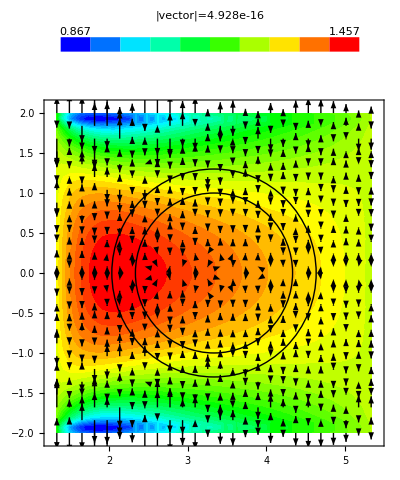

```mathematica
SectionRZ[Bxi,Byi,Bzi,0.2 π]
```

```mathematica
Show[GraphicsRow[{SectionRZ[Bxi,Byi,Bzi,0.6],SectionRΦ[Bxi,Byi,Bzi,Mean[bounds⟦3⟧],AspectRatio->Automatic],SectionΦZ[Bxi,Byi,Bzi,Mean[bounds⟦1⟧],AspectRatio->Automatic]},Spacings->Scaled[0.]],AspectRatio->1]
```

```mathematica
Show[GraphicsRow[{SectionRZ[jxi,jyi,jzi,0.3 π],SectionRΦ[jxi,jyi,jzi,Mean[bounds⟦3⟧]],SectionΦZ[jxi,jyi,jzi,Mean[bounds⟦1⟧]]},Spacings->Scaled[0.]],AspectRatio->1,ImageSize->1000]
```

#### Оценки закрутки

```mathematica
{vx,vy,vz}=Take[out,{2,4}-1];
```

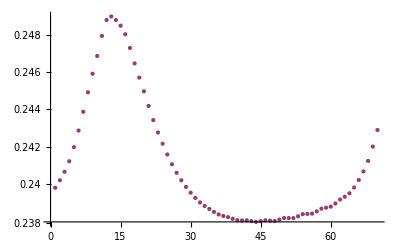

```mathematica
ListLogPlot[{Max/@Flatten/@Transpose[vx],√(Mean/@((Flatten/@Transpose[vz])^2))}]
```

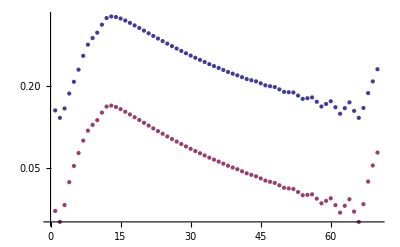

```mathematica
k
```

```mathematica
helicity=Total[MapThread[Times,{Take[out,3],rotd[Sequence@@Take[out,3],ghost]}]];
```

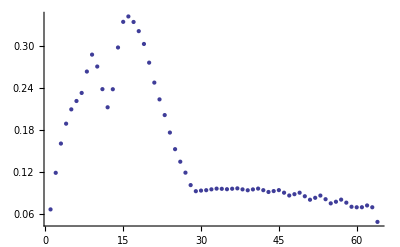

```mathematica
ListPlot[WithoutFict[Max/@Transpose[helicity]]]
```

```mathematica
phi=Outer[ArcTan,coor[[1]],coor[[3]]];
vphi=Table[vx[[All,ny,All]]Sin[phi]-vz[[All,ny,All]]Cos[phi],{ny,Dimensions[vx][[2]]}];
vrho=Table[vx[[All,ny,All]]Cos[phi]+vz[[All,ny,All]]Sin[phi],{ny,Dimensions[vx][[2]]}];
```

```mathematica
PrintRange[Max/@Flatten/@Transpose[vy]]
```

```mathematica
Fit[Take[Transpose[{coor[[2]],Log/@Max/@Flatten/@vphi}],{10,19}],{1,z},z]
```

0.120886-0.0254404 z

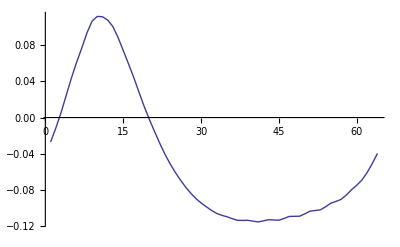

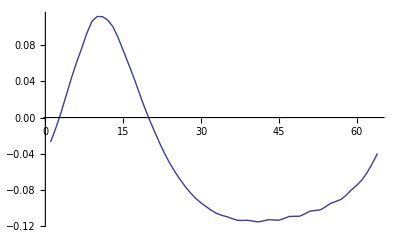

```mathematica
PrintRange[Log/@Max/@Flatten/@WithoutFict@vphi]
PrintRange[Log/@Max/@Flatten/@WithoutFict@vrho]
```

#### Графики сечений

```mathematica
DrawSection[Sequence@@Take[out,{2,4}-1],PointOfSections->{0.5,0,0}]
```

```mathematica
DrawSection[Bx,By,Bz,PointOfSections->{0.5,0,0}]
```

```mathematica
DrawSection[jx,jy,jz,PointOfSections->{0.5,0,0}]
```

```mathematica
PrintRange[WithoutFict@Bx⟦10,All,25⟧]
```

```mathematica
PrintRange[Take[Abs@Fourier@WithoutFict@Bx⟦15,All,15⟧,10]]
```

```mathematica
ReadDrawSection["dynamo_2_12820.snp",Binary,8,{5,6,7}]
```

```mathematica
DrawSection[Sequence@@ReadSection[4314]]
```

```mathematica
Table[ListPlot3D[Cut3D[Az,2,i],PlotRange->All],{i,1,Dimensions[By][[2]]}]
```

#### Чтение вдоль снэпов

```mathematica
Clear[ReadSection];
ReadSection[iter_,κ_Real:0,fluct_Symbol:False]:=Block[{dump,str=ToString[iter],Ax,Ay,Az},
(*While[StringLength[str]<5,str="0"<>str];*)
(*dump=.;ReadBinarySnapFiles["dynamo_","_"<>str<>".snp",5,dump,PrintInfo->None];*)
dump=.;ReadBinarySnapFile["screw_4_"<>str<>".snp",6,dump,PrintInfo->None];
dump=Take[dump,{1,-1}];
(*Return[Take[dump,3]];*)
{coor,bounds}=ReadAuxFiles[{"coord"},ShiftVector->{If[κ>0,1/κ,0],0,0}];
{Ax,Ay,Az}=Take[dump,-3];
If[fluct,
{Ax,Ay,Az}-=Transpose[Table[coor⟦1,i⟧Cos[coor⟦2,j⟧]{Sin[coor⟦2,j⟧],Cos[coor⟦2,j⟧],0},{i,1,n1+2ghost},{j,1,n2+2ghost},{k,1,n3+2ghost}],{2,3,4,1}]];
{Bx,By,Bz}=rotd[Ax,Ay,Az,ghost];
(*{jx,jy,jz}=rotc[Bx,By,Bz,ghost];*)
Return[{Bx,By,Bz}];];
ReadSection[iter_,κ_Integer:0,fluct_Symbol:False]:=ReadSection[iter,κ+0.,fluct];
```

```mathematica
grtot={};
```

```mathematica
nameexp="parker";
```

Независимый код

```mathematica
Block[{g,dump},dump=ReadList["runtest1.dmp"];np=dump⟦3⟧;KolProc=Times@@np;dump=Drop[dump,{3}];{t,count,n1,n2,n3,Rey}=Take[dump,6];dump=Drop[dump,6];{pm,vxm,vym,vzm,Axm,Aym,Azm,nutm}=Transpose[Partition[dump,8]];ghost=1/(2 Last[np])(Total[(Last[Dimensions[#1]]&)/@CutList[pm,Last[np]]]-n3);coor=ReadList["coord",Number,RecordLists->True];bounds=({1/2 (#1⟦ghost⟧+#1⟦ghost+1⟧),1/2 (#1⟦-ghost⟧+#1⟦-ghost-1⟧)}&)/@coor;Ax=First[Fold[Map[Function[m,Clue[m,#2,ghost]],Partition[#1,np⟦#2⟧],{1}]&,Axm,{1,2,3}]];Ay=First[Fold[Map[Function[m,Clue[m,#2,ghost]],Partition[#1,np⟦#2⟧],{1}]&,Aym,{1,2,3}]];Az=First[Fold[Map[Function[m,Clue[m,#2,ghost]],Partition[#1,np⟦#2⟧],{1}]&,Azm,{1,2,3}]];{Ax,Ay,Az}-=Transpose[Table[coor⟦1,i⟧ Cos[coor⟦2,j⟧] {Sin[coor⟦2,j⟧],Cos[coor⟦2,j⟧],0},{i,1,n1+2 ghost},{j,1,n2+2 ghost},{k,1,n3+2 ghost}],{2,3,4,1}];{Bx,By,Bz}=rotc[Ax,Ay,Az,ghost];{jx,jy,jz}=rotc[Bx,By,Bz,ghost];{Bxi,Byi,Bzi,jxi,jyi,jzi}=(ListInterpolation[#1,{{Min[coor⟦1⟧],Max[coor⟦1⟧]},{Min[coor⟦2⟧],Max[coor⟦2⟧]},{Min[coor⟦3⟧],Max[coor⟦3⟧]}},InterpolationOrder->1]&)/@{Bx,By,Bz,jx,jy,jz};g=GraphicsRow[{SectionRZ[Bxi,Byi,Bzi,0.2 π],SectionRΦ[Bxi,Byi,Bzi,Mean[bounds⟦3⟧]],SectionΦZ[Bxi,Byi,Bzi,Mean[bounds⟦1⟧]]},Spacings->Scaled[0.],PlotLabel->"t="<>ToString[t]];
fname=nameexp<>"0000.gif";
Export[fname,g,ImageResolution->300,ImageSize->640];]
```

```mathematica
ReadSectionDraw2File[16522,0.75];
g1
```

```mathematica
ReadSectionDraw2File[iter_,κ_:0]:=Block[{fname},
{Bx,By,Bz}=ReadSection[iter,κ];
{coor,bounds}=ReadAuxFiles[{"coord"},ShiftVector->{0,0,0}];
g1=DrawSection[Bx,By,Bz];
fname="("<>ToString[κ]<>")screw"<>ToString[iter]<>"_B.gif";
Export[fname,g1,ImageResolution->300,ImageSize->640];
]
```

```mathematica
nums=Union[ToExpression[First[StringCases[#,RegularExpression["([^_]+?)_([^_]+?)_([^\\.]+?)\\.(.*?)"]->"$3"]]]&/@FileNames["*.snp"]]
```

{1880,1883,3728,5571,7430,9285,11143,13005,14874,16734,18590,20451,22309,24176,26039,27910,29758,31615,33471,35334,37200}

```mathematica
ReadSection[nums[[1]]]//Dimensions
```

{3,70,38,70}

```mathematica
infos=ScanSnaps;
```

Сетка одинаковая: {64,32,64}

Деление на процессы одинаковое: {4,2,8}

Структура у всех одинаковая

```mathematica
infos[[1]]
```

```mathematica
PrintRange[Sort@infos[[All,3]]]
```

```mathematica
lf1=lf2=lf3=lf4=lf5={};
Monitor[Do[Block[{Bx,By,Bz,g1,g2,fname},
{Bx,By,Bz}=ReadSection[nums⟦i⟧];
(*Print["have read ponom_"<>ToString[nums⟦i⟧]<>".snp"];*)
AppendTo[lf1,Fourier@WithoutFict@Bx⟦15,All,15⟧];
AppendTo[lf2,Fourier@(Total[Flatten[#^2]]&/@Transpose[WithoutFict@Bx,{2,1,3}])];
AppendTo[lf3,Fourier@(Total[Flatten[#^2]]&/@Transpose[WithoutFict@By,{2,1,3}])];AppendTo[lf4,Fourier@(Total[Flatten[#^2]]&/@Transpose[WithoutFict@Bz,{2,1,3}])];
],{i,1,Length[nums]}],nums⟦i⟧];
```

```mathematica
Manipulate[ListLogPlot[Take[Abs@lf1⟦i⟧,15],PlotRange->{10^-20,10^5},PlotLabel->infos[[i]]],{i,1,Length[nums],1}]
```

```mathematica
Monitor[Do[Block[{Bx,By,Bz,jx,jy,jz,g1,g2,fname},
{Bx,By,Bz}=ReadSection[nums⟦i⟧,0.25];
(*{jx,jy,jz}=rotc[Bx,By,Bz,3];*)
(*Print["have read ponom_"<>ToString[nums⟦i⟧]<>".snp"];*)
g1=DrawSection[Bx,By,Bz];
fname="screw"<>ToString[nums⟦i⟧]<>"_B.gif";
Export[fname,g1,ImageResolution->300,ImageSize->640];
(*g2=DrawSection[jx,jy,jz];
fname="ponom"<>ToString[nums⟦i⟧]<>"_j.gif";
Export[fname,g2,ImageResolution->300,ImageSize->640];*)
],{i,1,Length[nums]}],nums⟦i⟧];
```

```mathematica
res={};Monitor[Do[AppendTo[res,ReadSection[nums⟦i⟧,nproc]],{i,Length[nums]}],nums⟦i⟧]
```

```mathematica
Dimensions[res]
```

{400,3,38,38,38}

```mathematica
Do[Block[{g},
temp=First[Import["dynamo_2_"<>ToString[nums⟦i⟧]<>".snp.ZIP",{"*.snp","Binary"}]];
Export["dynamo_2_"<>ToString[nums⟦i⟧]<>".snp",temp,"Binary","DataFormat"-> "Byte"];
{Bx,By,Bz}=ReadSection[nums⟦i⟧];
Print["have read dynamo_2_"<>ToString[nums⟦i⟧]<>".snp"];
Close["dynamo_2_"<>ToString[nums⟦i⟧]<>".snp"];
DeleteFile["dynamo_2_"<>ToString[nums⟦i⟧]<>".snp"];
(*{Bxi,Byi,Bzi,jxi,jyi,jzi}=(ListInterpolation[#1,{{Min[coor⟦1⟧],Max[coor⟦1⟧]},{Min[coor⟦2⟧],Max[coor⟦2⟧]},{Min[coor⟦3⟧],Max[coor⟦3⟧]}},InterpolationOrder->1]&)/@{Bx,By,Bz,jx,jy,jz};g=DisplayTogetherArray[SectionRZ[Bxi,Byi,Bzi,0.2 π],SectionRΦ[Bxi,Byi,Bzi,Mean[bounds⟦3⟧]],SectionΦZ[Bxi,Byi,Bzi,Mean[bounds⟦1⟧]],Spacings->Scaled[0.],DisplayFunction->Identity,PlotLabel->"t="<>ToString[t]];*)
g=DrawSection[Bx,By,Bz];
fname="dynamo"<>ToString[nums⟦i⟧]<>".gif";Export[fname,g,ImageResolution->300,ImageSize->640];],{i,1,Length[nums]}];
```

```mathematica
Do[Block[{g},
temp=First[Import["dynamo_2_"<>ToString[nums⟦i⟧]<>".snp.ZIP",{"*.snp","Binary"}]];
Export["dynamo_2_"<>ToString[nums⟦i⟧]<>".snp",temp,"Binary","DataFormat"-> "Byte"];
{Bx,By,Bz}=ReadSection[nums⟦i⟧];
Print["have read dynamo_2_"<>ToString[nums⟦i⟧]<>".snp"];
Close["dynamo_2_"<>ToString[nums⟦i⟧]<>".snp"];
DeleteFile["dynamo_2_"<>ToString[nums⟦i⟧]<>".snp"];
(*{Bxi,Byi,Bzi,jxi,jyi,jzi}=(ListInterpolation[#1,{{Min[coor⟦1⟧],Max[coor⟦1⟧]},{Min[coor⟦2⟧],Max[coor⟦2⟧]},{Min[coor⟦3⟧],Max[coor⟦3⟧]}},InterpolationOrder->1]&)/@{Bx,By,Bz,jx,jy,jz};g=DisplayTogetherArray[SectionRZ[Bxi,Byi,Bzi,0.2 π],SectionRΦ[Bxi,Byi,Bzi,Mean[bounds⟦3⟧]],SectionΦZ[Bxi,Byi,Bzi,Mean[bounds⟦1⟧]],Spacings->Scaled[0.],DisplayFunction->Identity,PlotLabel->"t="<>ToString[t]];*)
g=DrawSection[Bx,By,Bz];
fname="dynamo"<>ToString[nums⟦i⟧]<>".gif";Export[fname,g,ImageResolution->300,ImageSize->640];],{i,1,Length[nums]}];
```

```mathematica
gr=Table[{Bx,By,Bz,jx,jy,jz}=ReadSection[i];{Bxi,Byi,Bzi,jxi,jyi,jzi}=(ListInterpolation[#1,{{Min[coor⟦1⟧],Max[coor⟦1⟧]},{Min[coor⟦2⟧],Max[coor⟦2⟧]},{Min[coor⟦3⟧],Max[coor⟦3⟧]}},InterpolationOrder->1]&)/@{Bx,By,Bz,jx,jy,jz};DisplayTogetherArray[SectionRZ[Bxi,Byi,Bzi,0.2 π],SectionRΦ[Bxi,Byi,Bzi,Mean[bounds⟦3⟧]],SectionΦZ[Bxi,Byi,Bzi,Mean[bounds⟦1⟧]],Spacings->Scaled[0.],DisplayFunction->Identity],{i,10,2820,10}];
```

```mathematica
grtot=First/@gr
```

```mathematica
Export["current.gif",Show[#,DisplayFunction->Identity]&/@gr,ConversionOptions->{"AnimationDisplayTime"->0.2},ImageResolution->300,ImageSize->640];
```

#### Сложное рисование поверхностей

```mathematica
{cont1, cont2} = (0.1*{Max[#1], Min[#1]} & )[By]
```

```mathematica
bounds
```

```mathematica
cubic=Table[Block[{r=√(x^2+y^2),f=ArcTan[y,x+10^-10]+π},If[z≤bounds⟦3,2⟧∧z≥bounds⟦3,1⟧∧r≤bounds⟦1,2⟧∧r≥bounds⟦1,1⟧,Byi[r,f,z],0]],{z,-1.5,1.5,0.2},{x,-6,6,0.2},{y,-6,6,0.2}];
```

```mathematica
g1 = ColorLighting[ListContourPlot3D[cubic, Contours -> {cont1}, DisplayFunction -> Identity], {1, 0, 0}];
g2 = ColorLighting[ListContourPlot3D[cubic, Contours -> {cont2}, DisplayFunction -> Identity], {0, 0, 1}];
```

```mathematica
Show[g1, Lighting -> Automatic]
```

```mathematica
Show[Graphics3D[EdgeForm[]], g1, g2, Lighting -> None]
```

```mathematica
Show[Graphics3D[EdgeForm[]], ColorLighting[ListContourPlot3D[cubic, Contours -> {cont1}, DisplayFunction -> Identity], {1, 0, 0}], ColorLighting[ListContourPlot3D[cubic, Contours -> {cont2}, DisplayFunction -> Identity], {0, 0, 1}], Lighting -> None]
```

#### Простое рисование поверхностей

```mathematica
{min,max}={Max[#],Min[#]}&@helicity
```

{1.83789,-0.0597603}

```mathematica
val=By^2+Bx^2+Bz^2;
mx = Max[Abs@val]
{min,max}=mx{-1,1};
```

0.0000620332

```mathematica
val=out[[2]];
mx = Max[Abs@val]
{min,max}={0,mx};
```

1.49676

```mathematica
gh = ListContourPlot3D[Transpose[val,{3,2,1}], Contours ->(min+max)/2+(max-min)/2 1/4{-1/2,1/2} , ContourStyle -> {Directive[Yellow, Opacity[0.8]], Directive[Pink, Opacity[0.8]]}, BoxRatios -> Automatic, Mesh -> False, AxesLabel -> {x, y, z}, DataRange -> bounds]
```

#### Просмотр массива типа ячеек и отражений

```mathematica
{node} = ReadAuxFiles[{"node"}];
```

```mathematica
Union[Flatten[node]]
```

```mathematica
coor[[1]]
```

```mathematica
ArrayPlot[Transpose[Map[BitAnd[Round[#1], 31] &, node, {2}]], FrameTicks -> True, Mesh -> True, Frame -> True]
```

```mathematica
flag = 8 + 64;
ListDensityPlot[Transpose[Map[BitAnd[Round[#1], flag] &, nm[[2]], {2}]]]
ListDensityPlot[Transpose[Map[BitAnd[Round[#1], flag] &, nm[[1]], {2}]]]
```

```mathematica
gc=Graphics[Circle[{n1/2+ghost,n1/2+ghost},n1/2]]
```

```mathematica
DisplayTogether[ListContourPlot[node], gc];
```